```mathematica
(*Hamiltonian and useful matrices definitions*)
```

```mathematica
ClearAll[h0];
h0[t_]={{0,-t,0,-t},{-t,0,-t,0},{0,-t,0,-t},{-t,0,-t,0}};
x=DiagonalMatrix[{1,0,-1,0}];
y=DiagonalMatrix[{0,1,0,-1}];
mp=x+I y;
mm=x-I y;
d2=TensorProduct[{1,-1,1,-1},{1,-1,1,-1}];
hz=TensorProduct[{1,-I,-1,I},{1,I,-1,-I}]-TensorProduct[{1,I,-1,-I},{1,-I,-1,I}];
```

```mathematica
MatrixForm[h0]
```

(0 | -t | 0 | -t
-t | 0 | -t | 0
0 | -t | 0 | -t
-t | 0 | -t | 0)

```mathematica
Conjugate[Transpose[mm]]-mp
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[mm]
```

(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ)

```mathematica
{1,-I,-1,+I}.mp.{1,1,1,1}
```

4

```mathematica
TensorProduct[{1,-1,1,-1},{1,-1,1,-1}]
```

{{1,-1,1,-1},{-1,1,-1,1},{1,-1,1,-1},{-1,1,-1,1}}

```mathematica
Eigenvalues[h0[1]+a Exp[I b] mm+a Exp[-I b] mp]/.a->1/.b->0.5
```

{-0.609316-5.55112×10^-17 ⅈ,0.609316+5.55112×10^-17 ⅈ,-2.76202+2.22045×10^-16 ⅈ,2.76202-2.22045×10^-16 ⅈ}

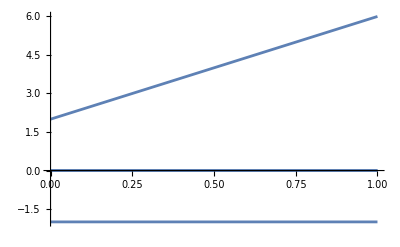

```mathematica
Plot[Eigenvalues[h0[1]+a TensorProduct[{1,-1,1,-1},{1,-1,1,-1}]],{a,0,1}]
```

```mathematica
Manipulate[Plot[Min[Eigenvalues[h0[1]+r Cos[p] x+r Sin[p] y+a2 TensorProduct[{1,-1,1,-1},{1,-1,1,-1}]]]+0.2r^2,{p,0,2Pi}],{r,0,3},{a2,0,10}]
```

```mathematica
Manipulate[Plot3D[Min[Eigenvalues[h0[1]+a x+b y+a2 TensorProduct[{1,-1,1,-1},{1,-1,1,-1}]]]+g(a^2+b^2),{a,-2,2},{b,-2,2}],{g,0,1},{a2,0,10}]
```

```mathematica
Manipulate[Plot3D[Min[Re[Eigenvalues[h0[1]+a Exp[I b] mm+a Exp[-I b] mp+a2 d2]]]+g(a^2),{a,-2,2},{b,-2,2}],{g,0,1},{a2,0,10}]
```

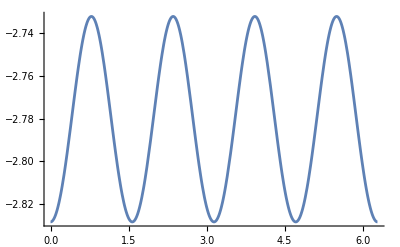

```mathematica
Plot[Min[Re[Eigenvalues[h0[1]+a Exp[I b] mm+a Exp[-I b] mp+0 d2]]]/.a->1,{b,0,2Pi}]
```

```mathematica
Plot[Min[Re[Eigenvalues[h0[1]+a Exp[I b] mm+a Exp[-I b] mp]]]/.a->1,{b,0,2Pi}]
```

-Graphics-

```mathematica
ClearAll[h0];
h0[t_]={{0,-t,0,-t},{-t,0,-t,0},{0,-t,0,-t},{-t,0,-t,0}};
x=DiagonalMatrix[{1,0,-1,0}];
y=DiagonalMatrix[{0,1,0,-1}];
mp=x+I y;
mm=x-I y;
d2=TensorProduct[{1,-1,1,-1},{1,-1,1,-1}];
hz=TensorProduct[{1,-I,-1,I},{1,I,-1,-I}]-TensorProduct[{1,I,-1,-I},{1,-I,-1,I}];
```

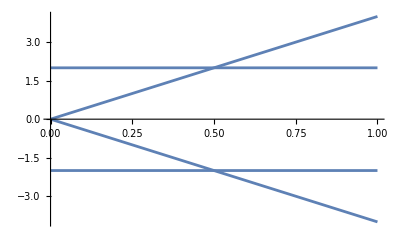

```mathematica
Plot[Sort[Eigenvalues[h0[1]+a hz]],{a,0,1}]
```

```mathematica
Manipulate[Plot3D[Min[Eigenvalues[h0[1]+a x+b y+a2 hz]]+g(a^2+b^2),{a,-1,1},{b,-1,1}],{g,0,1},{a2,0,10}]
```

```mathematica
(*Energy minimization function*)
```

```mathematica
c[a_?NumericQ,b_?NumericQ]=Min[Eigenvalues[h0[1]+a x+b y+h hz]]+g(a^2+b^2);
f[h_?NumericQ,g_?NumericQ]:=FindMinimum[Min[Eigenvalues[h0[1]+a x+b y+h hz]]+g(a^2+b^2),{{a,0.1},{b,0.3}}];
```

```mathematica
(*start with paraelectric*)
```

```mathematica
f[0,0.3]
```

Min::nord: Invalid comparison with Min[-2.,0.-2.10734×10^-8 ⅈ,0.+2.10734×10^-8 ⅈ,2.] attempted.

FindMinimum::nrnum: The function value 3.14608×10^-15+Min[-2.,0.-2.10734×10^-8 ⅈ,0.+2.10734×10^-8 ⅈ,2.] is not a real number at {a,b} = {9.61629×10^-8,3.52084×10^-8}.

{-2.,{a→9.29736×10^-8,b→4.12998×10^-8}}

```mathematica
b/.f[0,0.3][[2,2]]
```

Min::nord: Invalid comparison with Min[-2.,0.-2.10734×10^-8 ⅈ,0.+2.10734×10^-8 ⅈ,2.] attempted.

FindMinimum::nrnum: The function value 3.14608×10^-15+Min[-2.,0.-2.10734×10^-8 ⅈ,0.+2.10734×10^-8 ⅈ,2.] is not a real number at {a,b} = {9.61629×10^-8,3.52084×10^-8}.

4.12998×10^-8

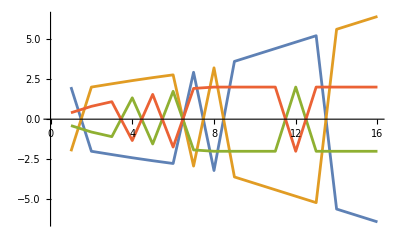

```mathematica
ListLinePlot[Transpose[Table[Eigenvalues[h0[1]+tab[[k]] y+0.1k hz],{k,1,16}]]]
```

```mathematica
Conjugate[Eigenvectors[h0[1]+tab[[1]] y+0.1 hz][[1]]].hz.Eigenvectors[h0[1]+tab[[1]] y+0.11 hz][[1]]
```

-5.62696×10^-15-4.88314×10^-23 ⅈ

```mathematica
Table[Conjugate[Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[1]]].hz.Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[1]],{k,1,16}]
```

{5.31211×10^-15+9.04688×10^-24 ⅈ,1.01311×10^-14+1.76354×10^-23 ⅈ,0.509303+4.92141×10^-17 ⅈ,1.18187+1.27688×10^-17 ⅈ,1.9352-5.55112×10^-17 ⅈ,2.73795-1.43663×10^-17 ⅈ,3.57332-6.72178×10^-18 ⅈ,4.-1.33495×10^-24 ⅈ,4.+3.48254×10^-24 ⅈ,4.+0. ⅈ,4.-6.62497×10^-25 ⅈ,4.-3.90161×10^-27 ⅈ,4.-6.52224×10^-25 ⅈ,4.-6.27278×10^-25 ⅈ,4.+7.83899×10^-26 ⅈ,4.+3.69906×10^-26 ⅈ}

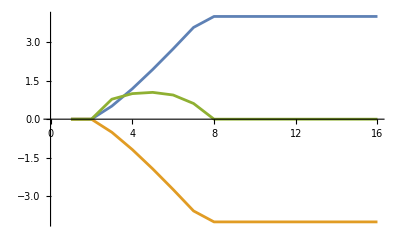

```mathematica
ListLinePlot[{Re[Table[Conjugate[Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[1]]].hz.Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[1]],{k,1,16}]],Re[Table[Conjugate[Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[2]]].hz.Eigenvectors[h0[1]+tab[[k]] y+0.1k hz][[2]],{k,1,16}]],tab}]
```

```mathematica
tab=ParallelTable[b/.f[0.1k,0.3][[2,2]],{k,1,16}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
ParallelTable[b/.f[0.1k,0.3][[2,2]],{k,1,16}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.56455×10^-7,1.33683×10^-7,0.777611,0.995284,1.04373,0.941285,0.611118,1.04502×10^-7,7.99263×10^-8,4.55508×10^-8,9.26955×10^-8,-2.00358×10^-8,-1.43493×10^-7,-1.10999×10^-7,-1.25344×10^-8,-9.73231×10^-9}

```mathematica
ParallelTable[a/.f[0.1k,0.3][[2,1]],{k,1,16}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.65137×10^-7,-6.62956×10^-7,2.39188×10^-8,1.17228×10^-8,2.10798×10^-7,2.3692×10^-7,1.09179×10^-7,-8.94595×10^-8,-1.76141×10^-8,5.29503×10^-9,1.58752×10^-9,-1.35903×10^-8,-1.67623×10^-7,-6.50506×10^-8,4.54025×10^-8,-2.09927×10^-8}

```mathematica
(*start with ferroelectric*)
```

```mathematica
f[0,0.1]
```

{-2.9,{a→-2.14158×10^-8,b→4.58258}}

```mathematica
tab
```

{4.57347,4.5458,4.49855,4.43003,4.3379,4.21913,4.06983,3.88493,3.65749,3.37747,3.02888,2.58263,1.9719,0.907615,6.94377×10^-7,2.00357×10^-7}

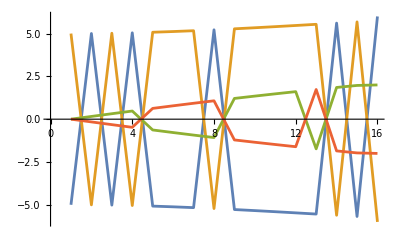

```mathematica
ListLinePlot[Transpose[Table[Eigenvalues[h0[1]+tab[[k]] y+0.1(k-1) hz],{k,1,16}]]]
```

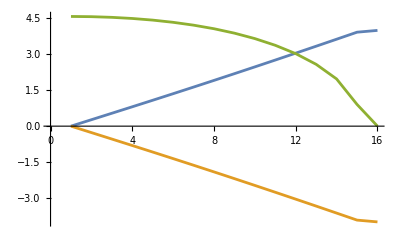

```mathematica
ListLinePlot[{Re[Table[Conjugate[Eigenvectors[h0[1]+tab[[k]] y+0.1(k-1) hz][[1]]].hz.Eigenvectors[h0[1]+tab[[k]] y+0.1(k-1) hz][[1]],{k,1,16}]],Re[Table[Conjugate[Eigenvectors[h0[1]+tab[[k]] y+0.1(k-1) hz][[2]]].hz.Eigenvectors[h0[1]+tab[[k]] y+0.1(k-1) hz][[2]],{k,1,16}]],tab}]
```

```mathematica
tab2
```

{-2.75462×10^-8,-9.50347×10^-8,1.16966×10^-8,-6.43042×10^-8,-4.9325×10^-9,-8.2889×10^-8,-1.42589×10^-7,-2.90797×10^-7,4.41975×10^-8,1.85485×10^-7,-1.17566×10^-7,-3.05794×10^-7,3.47396×10^-9,-8.08003×10^-7,0.0000104286,-9.50635×10^-7}

```mathematica
tab2=ParallelTable[a/.f[0.1(k-1),0.1][[2,1]],{k,1,16}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
tab=ParallelTable[b/.f[0.1(k-1),0.1][[2,2]],{k,1,16}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.